```mathematica
Clear["Global`*"]
sol=NDSolve[{x''[t]==-x'[t]+40*Sin[x[t]],x[0]==0.1,x''[0]==0},x,{t,0,5}];
```

```mathematica
xsol=x/.sol[[1]];
```

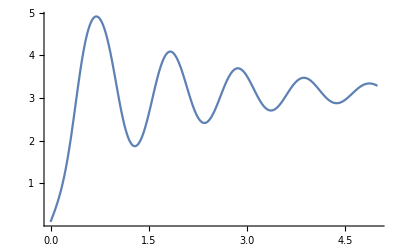

```mathematica
Plot[xsol[t],{t,0,5},PlotRange->All]
```